```mathematica
Quit[];
```

## Load and initialize HiggsTools

```mathematica
Install["/Path/To/HiggsTools/build/wstp/MHiggsTools"];
HSInitialize["/Path/To/HSDataSet"];
```

------------------------------------------------------------------------------

HiggsTools 1.0

H. Bahl, P. Bechtle, T. Biekoetter, S. Heinmeyer, S. Paasch,

C. Li, G. Weiglein, J. Wittbrodt

------------------------------------------------------------------------------

## Add SM - like Higgs boson

```mathematica
HPAddParticle["H",125.09,"neutral","even"]
```

## Evaluate Δχ^2

```mathematica
SetCharmCouplings[cc_,cct_,model_]:=HPEffectiveCouplingInput["H",uuRe->1,ddRe->1,ssRe->1,ccRe->cc,ccIm->cct,ttRe->1,bbRe->1,eeRe->1,mumuRe->1,tautauRe->1,ZZ->1,WW->1,gamgam->1,gg->1,Zgam->1,refModel->model,calcggH->False,calcHgamgam->False];

GetChisq[cc_,cct_,model_]:=(SetCharmCouplings[cc,cct,model];HSGetChisq[]);

calcDeltaChisq[list_,bound_:14.01]:=Module[{chisqmin,out},
chisqmin=Min[list[[;;,3]]];
out=list;
out[[;;,3]]-=chisqmin;
out=If[#[[3]]<bound,#,{#[[1]],#[[2]],bound}]&/@out;(* cut-off chisq value above bound for plotting *)
out
];
getMinChisq[list_]:=Module[{chisqmin,pos},
chisqmin=Min[list[[;;,3]]];
pos=Position[list[[;;,3]],chisqmin];
{list[[pos[[1,1]],1]],list[[pos[[1,1]],2]]}
];
```

```mathematica
resSMHiggs=calcDeltaChisq[Flatten[Table[{cc,cct,GetChisq[cc,cct,"SMHiggs"]},{cc,-3,3,.1},{cct,-3,3,.1}],1]];
resSMHiggsEW=calcDeltaChisq[Flatten[Table[{cc,cct,GetChisq[cc,cct,"SMHiggsEW"]},{cc,-3,3,.1},{cct,-3,3,.1}],1]];
```

```mathematica
minSMHiggs=getMinChisq[resSMHiggs];
minSMHiggsEW=getMinChisq[resSMHiggsEW];
```

## Plotting

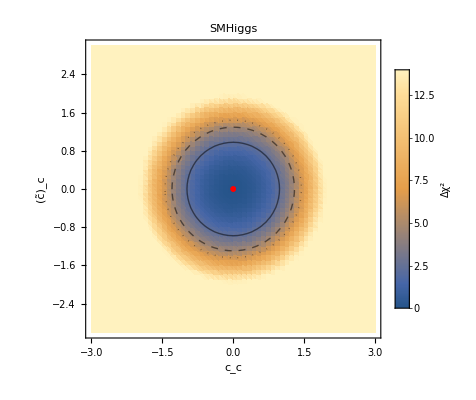

```mathematica
p1=ListDensityPlot[resSMHiggs,PlotLegends->BarLegend[Automatic,LegendLabel->"Δχ^2"],FrameLabel->{"c_c","(c̃)_c"},PlotLabel->"SMHiggs",PlotRange->{0,14.01}];
p2=ListContourPlot[resSMHiggs,Contours->{2.3,4.61,6.18},ContourShading->None,ContourStyle->{Thick,{Thick,Dashed},{Thick,Dotted}}];
p3=ListPlot[{minSMHiggs},PlotMarkers->{Text[Style["✶",20]]},PlotStyle->{Red}];
Show[p1,p2,p3]
```

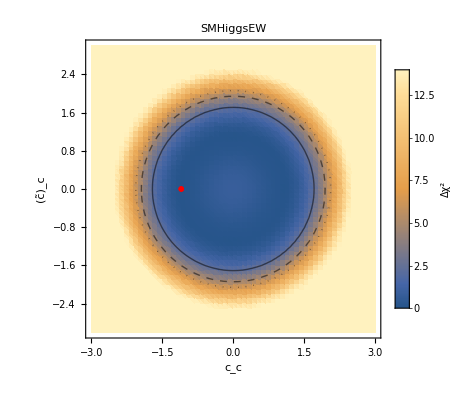

```mathematica
p1=ListDensityPlot[resSMHiggsEW,PlotLegends->BarLegend[Automatic,LegendLabel->"Δχ^2"],FrameLabel->{"c_c","(c̃)_c"},PlotLabel->"SMHiggsEW",PlotRange->{0,14.01}];
p2=ListContourPlot[resSMHiggsEW,Contours->{2.3,4.61,6.18},ContourShading->None,ContourStyle->{Thick,{Thick,Dashed},{Thick,Dotted}}];
p3=ListPlot[{minSMHiggsEW},PlotMarkers->{Text[Style["✶",20]]},PlotStyle->{Red}];
Show[p1,p2,p3]
```